#### 2. DOMAČA NALOGA (napredna računalniška orodja)

#### 1.1 Računanje vrednost π

#### Zahtevano : datotečna funkcija, uporabljene lokalne spremenljivke z uporaba okolja Module[]

```mathematica
Get["C:\\Users\\p s\\Desktop\\3._letnik_faksa\\Napredna_računalniška_orodja\\domače naloge\\2.d.n\\točke.m"]
```

```mathematica
Š=30000;

noter[n_]:=Module[{rx,ry,noter,točkee,razdalja},
noter={};
točkee=ztočke[n];
For[i=1,i<=Length[točkee],i++,
rx=točkee[[i,1]];
ry=točkee[[i,2]];
razdalja=Sqrt[rx^2+ry^2];
If[razdalja<=1,AppendTo[noter,{rx,ry}];]];
noter]
```

```mathematica
tkrog=noter[Š];
Noter=Length[noter[Š]];
```

```mathematica
(*Število π*)
pi=(4*Noter)/Š//N
```

3.1496

IZRIS

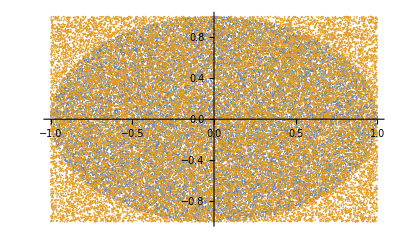

```mathematica
ListPlot[{tkrog,ztočke[Š]}]
```

#### 1.2) Razvoj v vrsto in funkcija Manipulate

```mathematica
f[t_]=Sin[t]*t^2*E^-t;
t0=2;
č=10;
```

```mathematica
vrsta=Series[f[t],{t,t0,č}];
norvrsta=Normal[%];
```

IZRIS

```mathematica
(*Eksaktna funkcija*)
p1=Plot[f[t],{t,0,4},PlotStyle->{Red},AxesLabel->{"t","f"}];
```

```mathematica
(*Vrsta/približek*)
p2=Plot[norvrsta,{t,0,4},PlotStyle->Dashed,AxesLabel->{"t","f"}];
```

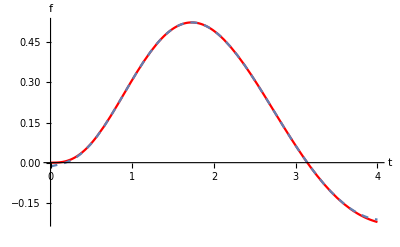

```mathematica
p1p2=Show[p1,p2]
```

IZRIS Z MOŽNOSTJO SPREMINJANJA REDA PRIBLIŽKA (n)

```mathematica
Manipulate[
Show[
Plot[Evaluate[Normal[Series[f[t],{t,t0,n}]]],{t,0,4}],
p1,
PlotRange->All,
AxesLabel->{"t","f"}],
{n,1,10,1}
]
```